```mathematica
points:=RandomReal[{0,10000},{20,2}](*20 point*)
```

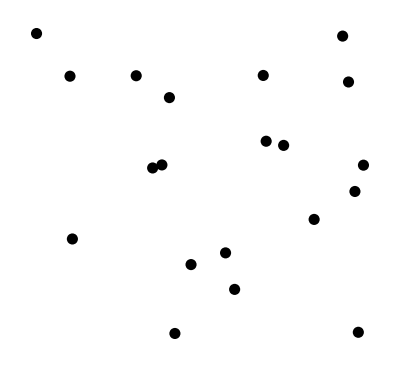

```mathematica
Graphics[{PointSize[0.02],Point[points]}]
```

```mathematica
Manipulate[
Graphics[{
Circle[{0,0},1],
Point[{Cos[theta],Sin[theta]}]
},PlotRange->{{-1.2,1.2},{-1.2,1.2}}],
{{theta,0,"Angle"},0,2Pi,Pi/20}
]
```

```mathematica
nodes={{0,0},{1,1}};
Graphics[{Black,PointSize[0.02],Point[nodes],Arrow[nodes]},
PlotRange->{{-1,2},{-1,2},Axis->True,Frame->False}]
```

-Graphics-

```mathematica
Opacity[25]
```

Opacity[25]